## Sim Data Bifurcation Plot

```mathematica
mg[tend_,param_]:=Module[{tdelay=2,init={x[0]==0.5},pars={β->param,γ->1,n->9.65}},
eq={x'[t]==(β x[t-tdelay])/(1+x[t-tdelay]^n)-γ x[t]};
NDSolveValue[{eq/.pars,init},{x},{t,0,tend}]
]
runs=Table[{i,mg[100,i][[1]]},{i,0,2,0.1}];
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of NDSolveValue::ihist will be suppressed during this calculation.

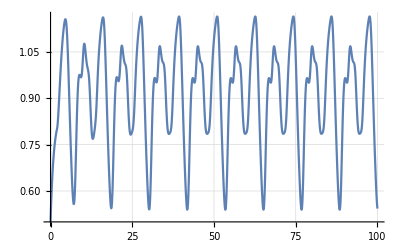

```mathematica
Plot[runs[[18,2]][x],{x,0,100},GridLines->Automatic]
Clear[runs]
```

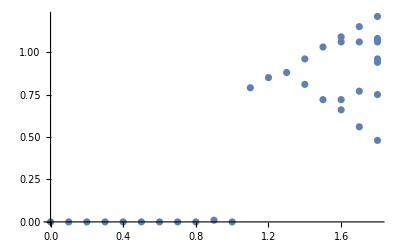

```mathematica
data={{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0.01},{1.0,0},{1.1,0.79},{1.2,0.85},{1.3,0.88},{1.4,0.81},{1.4,0.96},{1.5,0.72},{1.5,1.03},{1.6,0.66},{1.6,1.09},{1.6,0.72},{1.6,1.06},{1.7,1.15},{1.7,0.56},{1.7,1.06},{1.7,0.77},{1.8,1.21},{1.8,0.48},{1.8,0.96},{1.8,0.94},{1.8,1.08},{1.8,1.06},{1.8,1.07},{1.8,0.75}};
ListPlot[data]
Clear[data]
```

### Automation

```mathematica
Clear[peaks,data,ts,runs]
mg[td_,gain_]:=Module[{tdelay=td,init={x[0]==0.5},pars={β->gain,γ->1,n->9.65}},
eq={x'[t]==(β x[t-tdelay])/(1+x[t-tdelay]^n)-γ x[t]};
NDSolveValue[{eq/.pars,init},{x},{t,0,100}]
]
roundPeaks[ts_,tolerance_]:=Module[{},
Table[Round[ts[[i]],tolerance],{i,1,Length@ts}]//DeleteDuplicates
]
coarsePeakQ[ts_,j_,g_]:=Module[{},
If[(AllTrue[Table[ts[[k]],{k,j-g,j-1}],#<ts[[j]]&]&&AllTrue[Table[ts[[k]],{k,j+1,j+g}],#<ts[[j]]&])||(AllTrue[Table[ts[[k]],{k,j-g,j-1}],#>ts[[j]]&]&&AllTrue[Table[ts[[k]],{k,j+1,j+g}],#>ts[[j]]&]),ts[[j]],0]
]
getPeaks[data_,tolerance_:0.02,granularity_:1]:=Module[{ts=If[ListQ[data],data,Table[data[x],{x,0,100,0.1}]],peaks={}},
Monitor[For[i=3,i<Length@ts-3,i++,
AppendTo[peaks,coarsePeakQ[ts,i,granularity]]
],i];
roundPeaks[peaks//DeleteCases[0],tolerance]
]
bifurcationDataG[startG_,endG_,inc_]:=Module[{runs=Table[{i,mg[2,i][[1]]},{i,startG,endG,inc}]},
peaks=Table[getPeaks[runs[[i,2]]],{i,1,Length@runs}];
Flatten[Table[Table[{(n+startG-1)*inc,peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
bifurcationDataTd[startTd_,endTd_,inc_]:=Module[{runs=Table[{i,mg[i,2][[1]]},{i,startTd,endTd,inc}]},
peaks=Table[getPeaks[runs[[i,2]]],{i,1,Length@runs}];
Flatten[Table[Table[{(n+startTd-1)*inc,peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
```

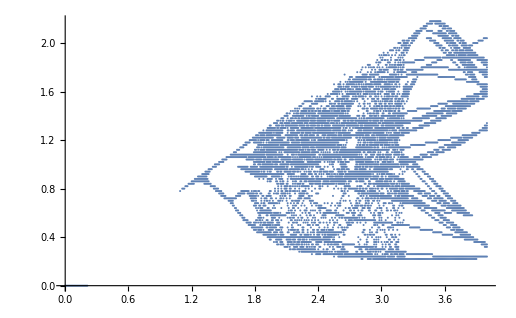

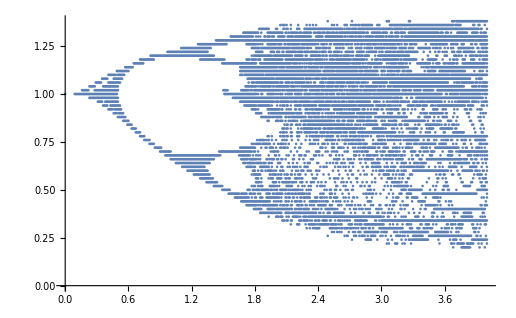

```mathematica
ListPlot[bifurcationDataG[0,4,0.01]]//Quiet
ListPlot[bifurcationDataTd[0,4,0.01]]//Quiet
```

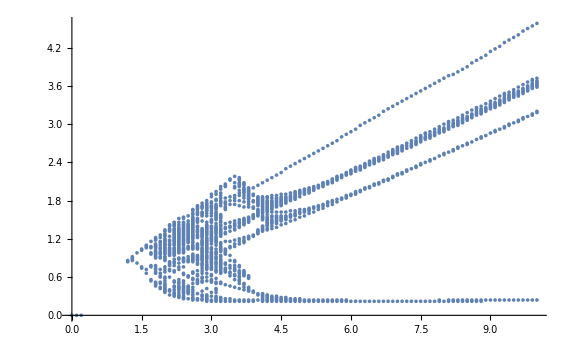

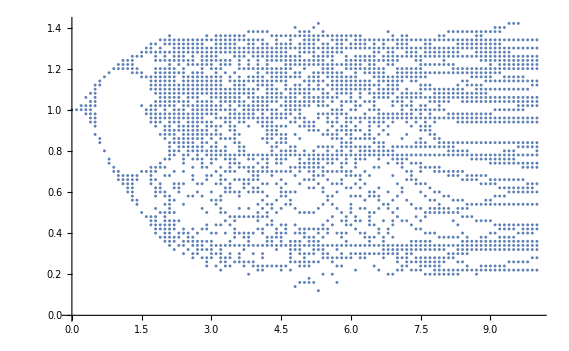

```mathematica
ListPlot[bifurcationDataG[0,10,0.1]]//Quiet
ListPlot[bifurcationDataTd[0,10,0.1]]//Quiet
```

```mathematica
bifurcationDataGTd[startG_,endG_,td_,inc_]:=Module[{runs=Table[{i,mg[i,td][[1]]},{i,startG,endG,inc}]},
peaks=Table[getPeaks[runs[[i,2]]],{i,1,Length@runs}];
Flatten[Table[Table[{td,(n+startG-1)*inc,peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
```

```mathematica
bifPlot3d=Flatten[Table[bifurcationDataGTd[0,4,i,0.1],{i,0,4,0.1}],1];//Quiet
ListPointPlot3D[bifPlot3d]
```

-Graphics3D-

## Real Data

```mathematica
Clear[peaks,data,ts,fixedData]
importData[basePath_,var_,start_,stop_,inc_]:=Module[{files=Table[basePath<>ToString[i]<>var<>".csv",{i,start,stop,inc}]},
Table[fixData[Import[files[[i]],"CSV"]],{i,1,Length@files}]
]
fixData[csv_]:=Module[{},
Table[csv[[j,5]],{j,1,Length@csv}]
]
realBifurcationData[fixedData_,start_,inc_,tolerance_,granularity_]:=Module[{},
peaks=Table[getPeaks[fixedData[[i]],tolerance,granularity],{i,1,Length@fixedData}];
Flatten[Table[Table[{(n+start-1)*inc,peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
```

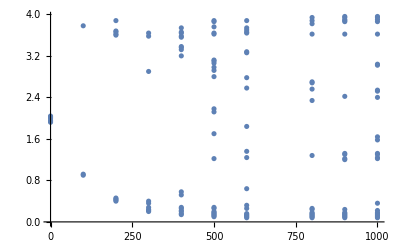

```mathematica
ListPlot[realBifurcationData[importData["D:\\F20\\Nonlinear Optoelectronic Dynamics\\Week 5\\MG_CSVs\\mgfb_","d",0,1000,100],0,100,0.02,5]]//Quiet
```

## Linear Piecewise MG Approximation

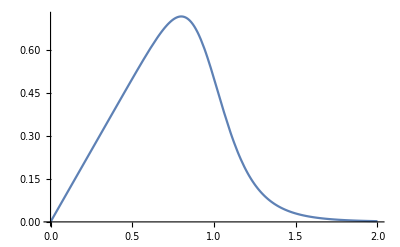

-(a c x^c)/((1+x^c)^2)+a/(1+x^c)

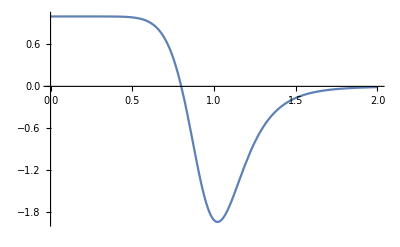

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.79965

1.3

```mathematica
Clear[a,c,x]
mgr[a_,c_,x_]:=(a x)/(1+x^c)
Plot[mgr[1,9.65,x],{x,0,2}]

dmg[a_,c_,x_]=D[mgr[a,c,x],x]
Plot[dmg[1,9.65,x],{x,0,2}]
peak=Solve[dmg[1,9.65,x]==0,x][[1,1,2]]
base=1.3
```

Piecewise[{{0, x<0}, {#a x, x<peak}, {lin[#a]⟦1⟧+lin[#a]⟦2,1⟧ x, x>peak&&x<base}, {0, x>base}}]&

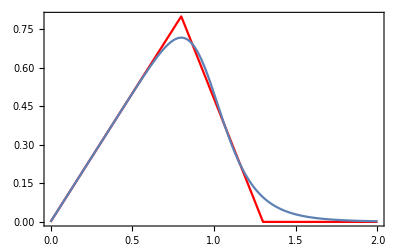

```mathematica
Clear[z]
lin[a_]:=Module[{},
Normal[LinearModelFit[{{peak,a peak},{base,0}},{1,z},z]]
]
mgp=Piecewise[{{0,x<0},{#a x,x<peak},{lin[#a][[1]]+lin[#a][[2,1]]x,x>peak&&x<base},{0,x>base}}]&
Show[Plot[mgp[<|"a"->1,"c"->9.65|>],{x,0,2},PlotStyle->Red,Frame->True,Axes->False],Plot[mgr[1,9.65,x],{x,0,2}]]
```

```mathematica
mgp[<|"a"->1,"c"->9.65|>]/.{x->0.98}
mgp[<|"a"->1,"c"->9.65|>]
```

0.511418

Piecewise[{{0, x<0}, {x, x<0.79965}, {2.07763-1.59818 x, x>0.79965&&x<1.3}, {0, True}}]

```mathematica
mgSim[td_,gain_,exp_]:=Module[{tdelay=td,init={x[0]==0.5},pars={β->gain,γ->1,n->exp}},
eq={x'[t]==(mgp[<|"a"->gain,"c"->exp|>]/.{x->x[t-tdelay]})-γ x[t]};
NDSolveValue[{eq/.pars,init},{x},{t,0,100}]
]
```

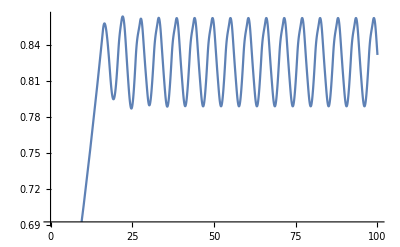

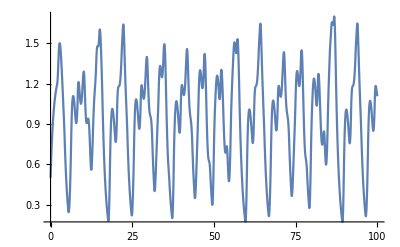

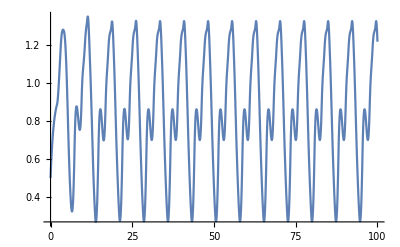

```mathematica
simP=mgSim[2,1.1,9.65][[1]];//Quiet
simC=mgSim[2,2.6,9.65][[1]];//Quiet
simP2=mgSim[2,1.9,9.65][[1]];//Quiet

Plot[simP[z],{z,0,100}]
Plot[simC[z],{z,0,100}]
Plot[simP2[z],{z,0,100}]
```

## Piecewise Bifurcation Plots

```mathematica
bifurcationDataGP[startG_,endG_,inc_]:=Module[{runs=Table[{i,mgSim[2,i,9.65][[1]]},{i,startG,endG,inc}]},
peaks=Table[getPeaks[runs[[i,2]]],{i,1,Length@runs}];
Flatten[Table[Table[{(n+startG-1)*inc,peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
bifurcationDataTdP[startTd_,endTd_,inc_]:=Module[{runs=Table[{i,mgSim[i,2,9.65][[1]]},{i,startTd,endTd,inc}]},
peaks=Table[getPeaks[runs[[i,2]]],{i,1,Length@runs}];
Flatten[Table[Table[{(n+startTd-1)*inc,peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
```

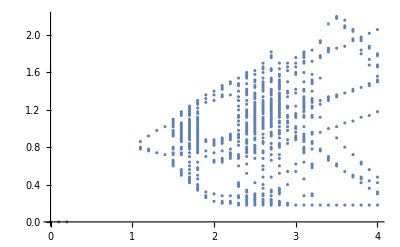

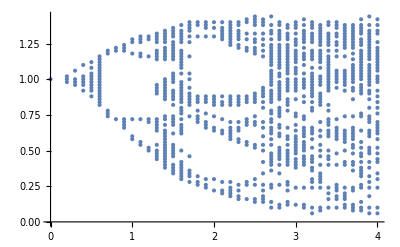

```mathematica
ListPlot[bifurcationDataGP[0,4,0.1]]//Quiet
ListPlot[bifurcationDataTdP[0,4,0.1]]//Quiet
```

## Autocorrelation and Power Spectra

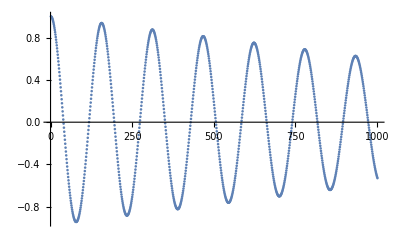

-Graphics3D-

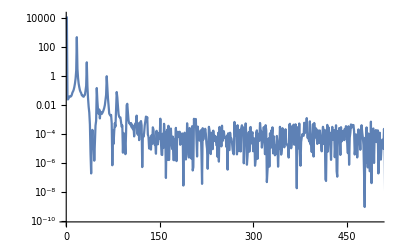

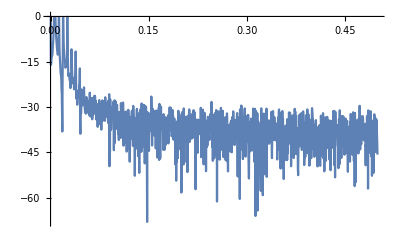

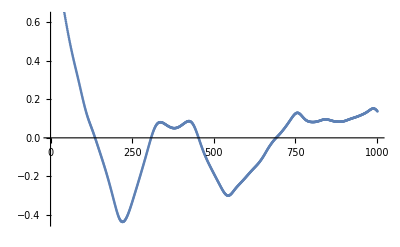

-Graphics3D-

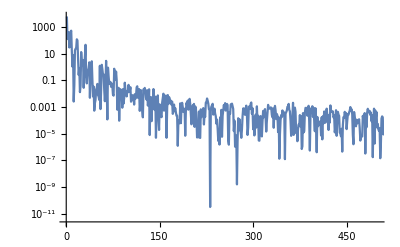

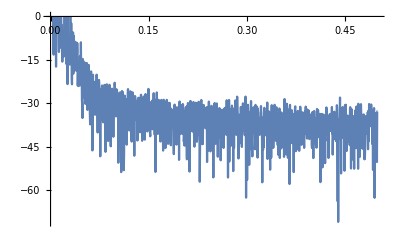

```mathematica
realData=importData["D:\\F20\\Nonlinear Optoelectronic Dynamics\\Week 5\\MG_CSVs\\mgfb_","d",0,1000,100];//Quiet
ListPlot[CorrelationFunction[realData[[2]],{1000}]]
ListPointPlot3D[Table[{realData[[2,i]],realData[[2,i-75]],realData[[2,i-150]]},{i,151,Length@realData[[2]]-151}]]
realFftP=Fourier[realData[[2]]];
ListLogPlot[Table[Re[realFftP[[i]]]^2,{i,1,Length@realFftP}],PlotRange->{{0,500},All},Joined->True]
Periodogram[realData[[2]]]
ListPlot[CorrelationFunction[realData[[9]],{1000}]]
ListPointPlot3D[Table[{realData[[2,i]],realData[[2,i-200]],realData[[2,i-400]]},{i,401,Length@realData[[2]]-401}]]
realFftC=Fourier[realData[[9]]];
ListLogPlot[Table[Re[realFftC[[i]]]^2,{i,1,Length@realFftC}],PlotRange->{{0,500},All},Joined->True]
Periodogram[realData[[9]]]
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

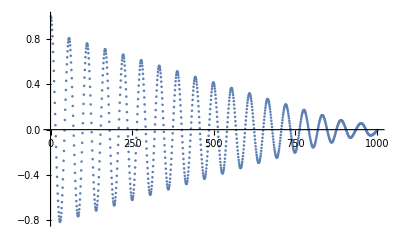

-Graphics3D-

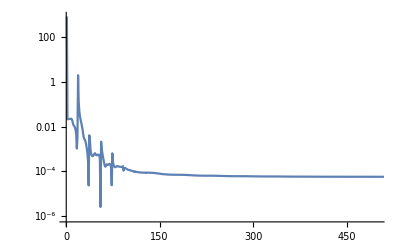

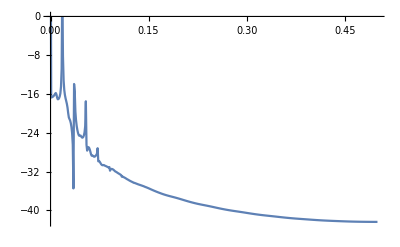

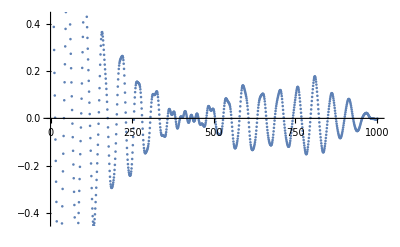

-Graphics3D-

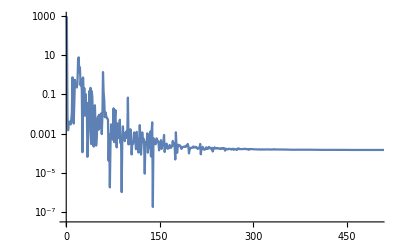

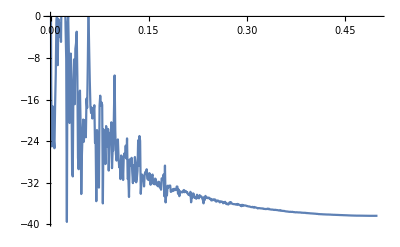

```mathematica
mgPeriodic=mg[2,1.5][[1]];
mgPeriodic=Table[mgPeriodic[x],{x,0,100,0.1}];
mgChaotic=mg[2,2.5][[1]];
mgChaotic=Table[mgChaotic[x],{x,0,100,0.1}];
ListPlot[CorrelationFunction[mgPeriodic,{1000}]]
ListPointPlot3D[Table[{mgPeriodic[[i]],mgPeriodic[[i-25]],mgPeriodic[[i-50]]},{i,51,Length@mgPeriodic-51}]]
simFftP=Fourier[mgPeriodic];
ListLogPlot[Table[Re[simFftP[[i]]]^2,{i,1,Length@simFftP}],PlotRange->{{0,500},All},Joined->True]
Periodogram[mgPeriodic]
ListPlot[CorrelationFunction[mgChaotic,{1000}]]
ListPointPlot3D[Table[{mgChaotic[[i]],mgChaotic[[i-75]],mgChaotic[[i-150]]},{i,151,Length@mgChaotic-151}]]
simFftC=Fourier[mgChaotic];
ListLogPlot[Table[Re[simFftC[[i]]]^2,{i,1,Length@simFftC}],PlotRange->{{0,500},All},Joined->True]
Periodogram[mgChaotic]
```

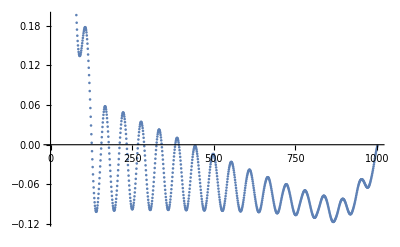

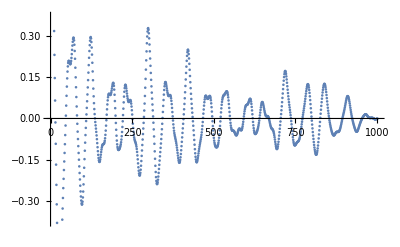

```mathematica
simP=mgSim[2,1.1,9.65][[1]];//Quiet
simC=mgSim[2,2.6,9.65][[1]];//Quiet
ListPlot[CorrelationFunction[Table[simP[x],{x,0,100,0.1}],{1000}]]
ListPlot[CorrelationFunction[Table[simC[x],{x,0,100,0.1}],{1000}]]
```

The real data provided much cleaner time delay embedding plots and autocorrelation function minima, probably because there is not a long enough time span to start getting messy like the simulated data does.

For the power spectra, the real data is more blurry whereas the simulated data gives a very nice example of the transition from clean peaks in the periodic regions and more blurring in the chaotic regions.